# Merged sequences Calculation of θ(t), dθ(t) and ν(t) dependences for heteropolymers with given sesquences and given product of transfer-matrices

## Preliminary chosen data and calculations

```mathematica
(*== Notes: 
F-> "f" in the program, c-> "conc, c" in the program, N -> "n"  in the program==*)

(*== Transfer matrix for heteropolymer: M[]  ==*)
M[d_,q_,W_]:=
Normal[SparseArray[{ {1,1}->W,{d-1,d}->(q-1),{d,d}->(q-1),{i_,j_}/;j-i==1-> 1,{d,j_}-> 1},{d,d}]]; 

(*==  Eigenvalues: λ for st-the highest value Subscript[λ, 1] second high value:Subscript[λ, 2]  ==*)
ML[d_,q_,W_]:=ML[d,q,W]=Eigenvalues[M[d,q,W]];(*λ*)
ML1[d_,q_,W_]:=Abs[ML[d,q,W][[1]]];(* Subscript[λ, 1]*)
ML2[d_,q_,W_]:=Abs[ML[d,q,W][[2]]]; (* Subscript[λ, 2]*)

(*==  Energetic parameter  ==*)
W[u_,t_]:=ⅇ^(u/t);



(*==  Correlation length  ==*)
Xi[d_,q_,W_]:=Abs[1/Log[ML1[d,q,W]/ML2[d,q,W]]];


(*==  Left matrix  &  right matrix  ==*)
MA[d_,q_,W_]:=Transpose[Eigenvectors[M[d,q,W]]];(*left matrix*)
MB[d_,q_,W_]:=Inverse[MA[d,q,W]];(*right matrix*)


(*==  Trasfer matrix of monomer in helix state: G' ==*)
 DW[d_,q_,W_]:=Normal[SparseArray[{ {1,1}->W},{d,d}]];  


(*== 2 differentials of characteristic equastion (L==λ -> variable) ==*)
dfdL[d_,L_, J_, Q_]:=L^(-1+d) (-ⅇ^J+L)+L^(-1+d) (L-Q)+(-1+d) L^(-2+d) (-ⅇ^J+L) (L-Q);
dfdJ[d_,L_, J_, Q_]:=ⅇ^J (1-Q)-ⅇ^J L^(-1+d) (L-Q);
dfdL[d_,q_,w_]:=dfdL[d,ML1[d,q,w],Log[w],q];dfdJ[d_,q_,w_]:=dfdJ[d,ML1[d,q,w],Log[w],q];


(*== Helicity degree: Theta1 and theta (different ways of calculation) ==*)
Theta1[d_,q_,W_]:=(MB[d,q,W]. DW[d,q,W].MA[d,q,W])[[1,1]]/ML1[d,q,W];
Theta[d_,q_,W_]:=-dfdJ[d,q,W]/dfdL[d,q,W]/ML1[d,q,W];
```

```mathematica
(*== values ==*)
(*== x-> probability of type A repeated units ,
	n0-> preliminary chosen number of repeated units,
	d-> transfer matrix dimension,
	u-> hydrogen bond's energy for A type and B type repeated units respectively-> u={Subscript[u, A],Subscript[u, B]},
	q-> number of conformations of repeated units: type A and type B respectively -> q={Subscript[q, A],Subscript[q, B]},
	t-> reduced temperature,
	data0 -> generating random sequence with probability "x"
 ==*)
d=4; u={1,0.8};q={71,51}; 

n=30000;ust={0.2,0.1};udst={0.1,0.2};
 qst={12,10}; qdst={10,12};
(* tmin=0.2; tmax=0.225; dt=(tmax-tmin)/500; look down for time propertie*)T={};
```

```mathematica
Creating an array of pseudorandom numbers corresponding to the sequences ;
seqord=RandomSample[Range[101,120],10]
```

```mathematica
{110,105,114,118,104,106,102,119,120,111}
```

```mathematica
(*-- Importing sequence --*)
seq1=Flatten[Import["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/110seq.dat"]];
(*-- Importing 2nd sequence --*)
seq2=Flatten[Import["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/105seq.dat"]];

(*-- Importing 3d sequence --*)
seq3=Flatten[Import["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_solvent/114seq.dat"]];
seq4=Flatten[Import["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_solvent/118seq.dat"]];
seq5=Flatten[Import["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_solvent/104seq.dat"]];
seq6=Flatten[Import["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_solvent/106seq.dat"]];
seq7=Flatten[Import["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_solvent/102seq.dat"]];
seq8=Flatten[Import["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_solvent/119seq.dat"]];
seq9=Flatten[Import["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_solvent/120seq.dat"]];
seq10=Flatten[Import["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_solvent/111seq.dat"]];


seqintr={};
(*--  merging sequences  --*)
AppendTo[seqintr,{seq1,seq2,seq3, seq4, seq5, seq6, seq6, seq7, seq8, seq9, seq10}];

(*-- making sequence as a normal matrix --*)
seq=Flatten[seqintr];

n=Length[seq];
```

```mathematica
conc=N[1/n Count[seq,0]]; (*concentration of type A nucleotides in the sequence*)

L1=ArrayFlatten[{{Normal[SparseArray[{{i_,j_}/;i==j-> 1},{d,d}]],Normal[ SparseArray[{{1,1}-> 0},{d,d}]]}}];
R1=Flatten[{Normal[SparseArray[{{i_,j_}/;i==j-> 1},{d,d}]],Normal[ SparseArray[{{1,1}-> 0},{d,d}]]},1];
R2=Flatten[{Normal[ SparseArray[{{1,1}-> 0},{d,d}]],Normal[SparseArray[{{i_,j_}/;i==j-> 1},{d,d}]]},1];
```

```mathematica
Importing tensors for random sequences                                        ;

Htensor01=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/50Htr.dat"];
Jtensor01=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/1Jtr.dat"];
Htensor02=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/46Htr.dat"];
Jtensor02=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/2Jtr.dat"];
Htensor03=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/53Htr.dat"];
Jtensor03=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/3Jtr.dat"];
Htensor04=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/49Htr.dat"];
Jtensor04=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/4Jtr.dat"];
Htensor05=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/52Htr.dat"];
Jtensor05=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/5Jtr.dat"];
Htensor06=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/48Htr.dat"];
Jtensor06=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/16Jtr.dat"];
Htensor07=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/49Htr.dat"];
Jtensor07=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/17Jtr.dat"];
Htensor08=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/54Htr.dat"];
Jtensor08=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/18Jtr.dat"];
Htensor09=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/55Htr.dat"];
Jtensor09=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/19Jtr.dat"];
Htensor10=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/51Htr.dat"];
Jtensor10=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/20Jtr.dat"];
T0=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/T0.dat"];
tmin=T0[[1]]; tmax=T0[[-1]]; dt=(tmax-tmin)/1000;
(*--  defines matrices to fill later   --*)
θ={};ν={};Htr01={};Htr02={};Htr03={};Htr04={};Htr05={};Htr06={};Htr07={};Htr08={};Htr09={};Htr10={};Jtr01={};
Jtr02={}; 
Jtr03={};Jtr04={};Jtr05={};Jtr06={};Jtr07={};Jtr08={};Jtr09={};Jtr10={};omega={};fi={}; ka={};
```

```mathematica
Importing tensors for  sequences with correlation                                ;

Htensor01=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/110Htr.dat"];
Jtensor01=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/21Jtr.dat"];
Htensor02=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/105Htr.dat"];
Jtensor02=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/22Jtr.dat"];
Htensor03=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/114Htr.dat"];
Jtensor03=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/23Jtr.dat"];
Htensor04=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/118Htr.dat"];
Jtensor04=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/24Jtr.dat"];
Htensor05=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/104Htr.dat"];
Jtensor05=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/25Jtr.dat"];
Htensor06=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/106Htr.dat"];
Jtensor06=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/26Jtr.dat"];
Htensor07=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/102Htr.dat"];
Jtensor07=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/27Jtr.dat"];
Htensor08=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/119Htr.dat"];
Jtensor08=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/28Jtr.dat"];
Htensor09=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/120Htr.dat"];
Jtensor09=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/29Jtr.dat"];
Htensor10=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/111Htr.dat"];
Jtensor10=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/30Jtr.dat"];
T0=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/T.dat"];
(*T01=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/T30+.dat"];
tmin=T0[[1]]; tmax=T0[[-1]]; dt=(tmax-tmin)/500;*)

(*--  defines matrices to fill later   --*)
θ={};ν={};Htr01={};Htr02={};Htr03={};Htr04={};Htr05={};Htr06={};Htr07={};Htr08={};Htr09={};Htr10={};Jtr01={};
Jtr02={}; 
Jtr03={};Jtr04={};Jtr05={};Jtr06={};Jtr07={};Jtr08={};Jtr09={};Jtr10={};omega={};fi={}; ka={};
```

```mathematica
Importing tensors for random sequences +solvent                                 ;

Htensor01=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/1Htr.dat"];
Jtensor01=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/1Jtr.dat"];
Htensor02=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/2Htr.dat"];
Jtensor02=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/2Jtr.dat"];
Htensor03=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/3Htr.dat"];
Jtensor03=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/3Jtr.dat"];
Htensor04=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/4Htr.dat"];
Jtensor04=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/4Jtr.dat"];
Htensor05=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/5Htr.dat"];
Jtensor05=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/5Jtr.dat"];
Htensor06=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/16Htr.dat"];
Jtensor06=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/16Jtr.dat"];
Htensor07=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/17Htr.dat"];
Jtensor07=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/17Jtr.dat"];
Htensor08=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/18Htr.dat"];
Jtensor08=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/18Jtr.dat"];
Htensor09=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/19Htr.dat"];
Jtensor09=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/19Jtr.dat"];
Htensor10=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/20Htr.dat"];
Jtensor10=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_solvent/20Jtr.dat"];
T0=Import[
"/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/random_seq/data_vacuum/T0.dat"];

tmin=T0[[1]]; tmax=T0[[-1]]; dt=(tmax-tmin)/1000;
(*--  defines matrices to fill later   --*)
θ={};ν={};Htr01={};Htr02={};Htr03={};Htr04={};Htr05={};Htr06={};Htr07={};Htr08={};Htr09={};Htr10={};Jtr01={};
Jtr02={}; 
Jtr03={};Jtr04={};Jtr05={};Jtr06={};Jtr07={};Jtr08={};Jtr09={};Jtr10={};omega={};fi={}; ka={};
```

```mathematica
Importing tensors for  sequences with correlation+solvent             ;

Htensor01=Import[
"/Users/arevikasatryan/Documents/Ae/aspirantura/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_solvent/21Htr.dat"];
Jtensor01=Import[
"/Users/arevikasatryan/Documents/Ae/aspirantura/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_solvent/21Jtr.dat"];
Htensor02=Import[
"/Users/arevikasatryan/Documents/Ae/aspirantura/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_solvent/22Htr.dat"];
Jtensor02=Import[
"/Users/arevikasatryan/Documents/Ae/aspirantura/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_solvent/22Jtr.dat"];
Htensor03=Import[
"/Users/arevikasatryan/Documents/Ae/aspirantura/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_solvent/23Htr.dat"];
Jtensor03=Import[
"/Users/arevikasatryan/Documents/Ae/aspirantura/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_solvent/23Jtr.dat"];
Htensor04=Import[
"/Users/arevikasatryan/Documents/Ae/aspirantura/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_solvent/24Htr.dat"];
Jtensor04=Import[
"/Users/arevikasatryan/Documents/Ae/aspirantura/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_solvent/24Jtr.dat"];
Htensor05=Import[
"/Users/arevikasatryan/Documents/Ae/aspirantura/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/25Htr.dat"];
Jtensor05=Import[
"/Users/arevikasatryan/Documents/Ae/aspirantura/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/25Jtr.dat"];
Htensor06=Import[
"/Users/arevikasatryan/Documents/Ae/aspirantura/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_solvent/36Htr.dat"];
Jtensor06=Import[
"/Users/arevikasatryan/Documents/Ae/aspirantura/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_solvent/36Jtr.dat"];
Htensor07=Import[
"/Users/arevikasatryan/Documents/Ae/aspirantura/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/37Htr.dat"];
Jtensor07=Import[
"/Users/arevikasatryan/Documents/Ae/aspirantura/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_solvent/37Jtr.dat"];
Htensor08=Import[
"/Users/arevikasatryan/Documents/Ae/aspirantura/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_solvent/38Htr.dat"];
Jtensor08=Import[
"/Users/arevikasatryan/Documents/Ae/aspirantura/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_solvent/38Jtr.dat"];
Htensor09=Import[
"/Users/arevikasatryan/Documents/Ae/aspirantura/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_solvent/39Htr.dat"];
Jtensor09=Import[
"/Users/arevikasatryan/Documents/Ae/aspirantura/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/39Jtr.dat"];
Htensor10=Import[
"/Users/arevikasatryan/Documents/Ae/aspirantura/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_solvent/40Htr.dat"];
Jtensor10=Import[
"/Users/arevikasatryan/Documents/Ae/aspirantura/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_solvent/40Jtr.dat"];
T0=Import[
"/Users/arevikasatryan/Documents/Ae/aspirantura/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/T0.dat"];
T01=Import[
"/Users/arevikasatryan/Documents/Ae/aspirantura/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/corr_seq/data_vacuum/T30+.dat"];
tmin=T0[[1]]; tmax=T0[[-1]]; dt=(tmax-tmin)/500;
(*--  defines matrices to fill later   --*)
θ={};ν={};Htr01={};Htr02={};Htr03={};Htr04={};Htr05={};Htr06={};Htr07={};Htr08={};Htr09={};Htr10={};Jtr01={};
Jtr02={}; 
Jtr03={};Jtr04={};Jtr05={};Jtr06={};Jtr07={};Jtr08={};Jtr09={};Jtr10={};omega={};fi={}; ka={};
```

## Main calculations in cycle

```mathematica
For[i=9,i<8009,i+=8,

(*== For every realisation separating "H" transfer matrices for each temperature to calculate "theta" later==*)
Htr01={};
AppendTo[Htr01,{Htensor01[[i-8]],Htensor01[[i-7]],Htensor01[[i-6]],Htensor01[[i-5]],Htensor01[[i-4]],Htensor01[[i-3]],Htensor01[[i-2]],Htensor01[[i-1]]}];
H1=10^-500*ArrayFlatten[Htr01,1];
Htr02={};
AppendTo[Htr02,{Htensor02[[i-8]],Htensor02[[i-7]],Htensor02[[i-6]],Htensor02[[i-5]],Htensor02[[i-4]],Htensor02[[i-3]],Htensor02[[i-2]],Htensor02[[i-1]]}];
H2=10^-500*ArrayFlatten[Htr02,1];

Htr03={};
AppendTo[Htr03,{Htensor03[[i-8]],Htensor03[[i-7]],Htensor03[[i-6]],Htensor03[[i-5]],Htensor03[[i-4]],Htensor03[[i-3]],Htensor03[[i-2]],Htensor03[[i-1]]}];
H3=10^-500*ArrayFlatten[Htr03,1];
Htr04={};
AppendTo[Htr04,{Htensor04[[i-8]],Htensor04[[i-7]],Htensor04[[i-6]],Htensor04[[i-5]],Htensor04[[i-4]],Htensor04[[i-3]],Htensor04[[i-2]],Htensor04[[i-1]]}];
H4=10^-500*ArrayFlatten[Htr04,1];
Htr05={};
AppendTo[Htr05,{Htensor05[[i-8]],Htensor05[[i-7]],Htensor05[[i-6]],Htensor05[[i-5]],Htensor05[[i-4]],Htensor05[[i-3]],Htensor05[[i-2]],Htensor05[[i-1]]}];
H5=10^-500*ArrayFlatten[Htr05,1];
Htr06={};
AppendTo[Htr06,{Htensor06[[i-8]],Htensor06[[i-7]],Htensor06[[i-6]],Htensor06[[i-5]],Htensor06[[i-4]],Htensor06[[i-3]],Htensor06[[i-2]],Htensor06[[i-1]]}];
H6=10^-500*ArrayFlatten[Htr06,1];
Htr07={};
AppendTo[Htr07,{Htensor07[[i-8]],Htensor07[[i-7]],Htensor07[[i-6]],Htensor07[[i-5]],Htensor07[[i-4]],Htensor07[[i-3]],Htensor07[[i-2]],Htensor07[[i-1]]}];
H7=10^-500*ArrayFlatten[Htr07,1];
Htr08={};
AppendTo[Htr08,{Htensor08[[i-8]],Htensor08[[i-7]],Htensor08[[i-6]],Htensor08[[i-5]],Htensor08[[i-4]],Htensor08[[i-3]],Htensor08[[i-2]],Htensor08[[i-1]]}];
H8=10^-500*ArrayFlatten[Htr08,1];
Htr09={};
AppendTo[Htr09,{Htensor09[[i-8]],Htensor09[[i-7]],Htensor09[[i-6]],Htensor09[[i-5]],Htensor09[[i-4]],Htensor09[[i-3]],Htensor09[[i-2]],Htensor09[[i-1]]}];
H9=10^-500*ArrayFlatten[Htr09,1];
Htr10={};
AppendTo[Htr10,{Htensor10[[i-8]],Htensor10[[i-7]],Htensor10[[i-6]],Htensor10[[i-5]],Htensor10[[i-4]],Htensor10[[i-3]],Htensor10[[i-2]],Htensor10[[i-1]]}];
H10=10^-500*ArrayFlatten[Htr10,1];

(*
(*== For every realisation separating "J" transfer matrices for each temperature to calculate "nu" later==*)
Jtr01={};
AppendTo[Jtr01,{Jtensor01[[i-8]],Jtensor01[[i-7]],Jtensor01[[i-6]],Jtensor01[[i-5]],Jtensor01[[i-4]],Jtensor01[[i-3]],Jtensor01[[i-2]],Jtensor01[[i-1]]}];
J1=10^-500*ArrayFlatten[Jtr01,1];
Jtr02={};
AppendTo[Jtr02,{Jtensor02[[i-8]],Jtensor02[[i-7]],Jtensor02[[i-6]],Jtensor02[[i-5]],Jtensor02[[i-4]],Jtensor02[[i-3]],Jtensor02[[i-2]],Jtensor02[[i-1]]}];
J2=10^-500*ArrayFlatten[Jtr02,1];
Jtr03={};
AppendTo[Jtr03,{Jtensor03[[i-8]],Jtensor03[[i-7]],Jtensor03[[i-6]],Jtensor03[[i-5]],Jtensor03[[i-4]],Jtensor03[[i-3]],Jtensor03[[i-2]],Jtensor03[[i-1]]}];
J3=10^-500*ArrayFlatten[Jtr03,1];

Jtr04={};
AppendTo[Jtr04,{Jtensor04[[i-8]],Jtensor04[[i-7]],Jtensor04[[i-6]],Jtensor04[[i-5]],Jtensor04[[i-4]],Jtensor04[[i-3]],Jtensor04[[i-2]],Jtensor04[[i-1]]}];
J4=10^-500*ArrayFlatten[Jtr04,1];
Jtr05={};
AppendTo[Jtr05,{Jtensor05[[i-8]],Jtensor05[[i-7]],Jtensor05[[i-6]],Jtensor05[[i-5]],Jtensor05[[i-4]],Jtensor05[[i-3]],Jtensor05[[i-2]],Jtensor05[[i-1]]}];
J5=10^-500*ArrayFlatten[Jtr05,1];
Jtr06={};
AppendTo[Jtr06,{Jtensor06[[i-8]],Jtensor06[[i-7]],Jtensor06[[i-6]],Jtensor06[[i-5]],Jtensor06[[i-4]],Jtensor06[[i-3]],Jtensor06[[i-2]],Jtensor06[[i-1]]}];
J6=10^-500*ArrayFlatten[Jtr06,1];
Jtr07={};
AppendTo[Jtr07,{Jtensor07[[i-8]],Jtensor07[[i-7]],Jtensor07[[i-6]],Jtensor07[[i-5]],Jtensor07[[i-4]],Jtensor07[[i-3]],Jtensor07[[i-2]],Jtensor07[[i-1]]}];
J7=10^-500*ArrayFlatten[Jtr07,1];
Jtr08={};
AppendTo[Jtr08,{Jtensor08[[i-8]],Jtensor08[[i-7]],Jtensor08[[i-6]],Jtensor08[[i-5]],Jtensor08[[i-4]],Jtensor08[[i-3]],Jtensor08[[i-2]],Jtensor08[[i-1]]}];
J8=10^-500*ArrayFlatten[Jtr08,1];
Jtr09={};
AppendTo[Jtr09,{Jtensor09[[i-8]],Jtensor09[[i-7]],Jtensor09[[i-6]],Jtensor09[[i-5]],Jtensor09[[i-4]],Jtensor09[[i-3]],Jtensor09[[i-2]],Jtensor09[[i-1]]}];
J9=10^-500*ArrayFlatten[Jtr09,1];
Jtr10={};
AppendTo[Jtr10,{Jtensor10[[i-8]],Jtensor10[[i-7]],Jtensor10[[i-6]],Jtensor10[[i-5]],Jtensor10[[i-4]],Jtensor10[[i-3]],Jtensor10[[i-2]],Jtensor10[[i-1]]}];
J10=10^-500*ArrayFlatten[Jtr10,1];
(*--  2 same angular matrices to use later  --*)

*)

prod=ArrayFlatten[{{Normal[SparseArray[{{i_,j_}/;i==j-> 1},{d,d}]],Normal[ SparseArray[{{1,1}-> 0},{d,d}]]},{Normal[ SparseArray[{{1,1}-> 0},{d,d}]],Normal[SparseArray[{{i_,j_}/;i==j-> 1},{d,d}]]}}];
prod1=ArrayFlatten[{{Normal[SparseArray[{{i_,j_}/;i==j-> 1},{d,d}]],Normal[ SparseArray[{{1,1}-> 0},{d,d}]]},{Normal[ SparseArray[{{1,1}-> 0},{d,d}]],Normal[SparseArray[{{i_,j_}/;i==j-> 1},{d,d}]]}}];


(*--  for each t calculating multiplication of transfer-matrices (using product of transfer matrices for every realisation) to calculate helicity degree (θ) later  --*)




prod=prod.H1.H2.H3.H4.H5.H6.H7.H8.H9.H10(*.H3.H2.H1.H4.H5.H10.H6.H8.H9.H7*);

(*--  for each t calculating multiplication of transfer-matrices (using product of transfer matrices for every realisation) to calculate average length of helix region (ν) later  --*)
(*  prod1=prod1.J1.J2.J3.J4.J5.J6.J7.J8.J9.J10; *)

(*-- calculating "Trace (Shpur)" of multiplication: "Left matrix","product of transfer-matrices" and "Right matrix" --*)
Ω=Tr[L1.prod.R1];
Ψ=Tr[L1.prod.R2]; 
(*  Κ=Tr[L1.prod1.R2];  *)

(*-- using "i" and calculating the right place for temperature value in matrix of temperatures  --*)
j=(i-1)/8;

T1=Flatten[T0[[j]]];

(*T1=Flatten[T01[[j]]];*)

(*--  Collecting θ(t) and ν(t) data respectively  --*)
AppendTo[θ,{T1[[1]],Θ=1/n*Ψ/Ω}];

(*  AppendTo[ν,{T1[[1]],nu=1/(1-Κ/Ψ)}];  *)
AppendTo[omega,Ω];
AppendTo[fi,Ψ]
(*  AppendTo[ka,Κ];  *)

]
```

## Graphs

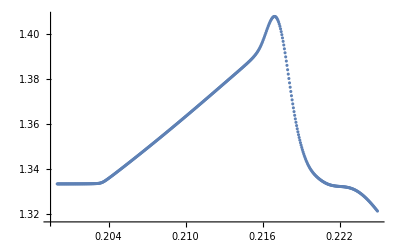

```mathematica
(*--  ν(t)dependence  --*)
nu1=ListPlot[ν]
```

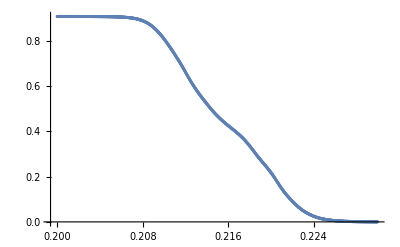

```mathematica
(*--  θ(t)dependence  --*)
T=ListPlot[θ]
```

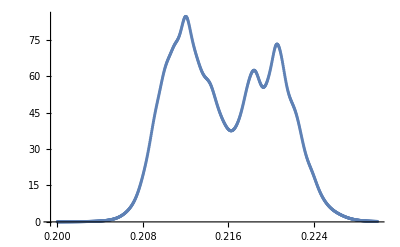

```mathematica
dθ=Table[{θ[[i,1]],-(θ[[i+1,2]]-θ[[i,2]])/(θ[[i+1,1]]-θ[[i,1]])},{i,Length[θ]-1}];

(*--  dθ(t)dependence  --*)
P=ListPlot[dθ, PlotRange->All]
```

## Exporting data

```mathematica
(*==  Exporting sequence  ==*)
strm=OpenWrite["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/merged_seq/random/vacuum/" <>  DateString[Date[],{"merged_seq"}]<>".dat"];
WriteString[strm,ExportString[seq,"TSV"]];(* "TSV"  "CSV" *)
Close[strm];
```

```mathematica
(*--  exporting data θ(t)  --*)
strm=
OpenWrite["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/merged_seq/random/vacuum/" <>  DateString[Date[],{"theta_t_merged"}]<>".dat"];
WriteString[strm,ExportString[θ,"TSV"]];(* "TSV"  "CSV" *)
Close[strm];
```

```mathematica
(*--  exporting data dθ(t)  --*)strm=OpenWrite["/Users/arevikasatryan/Documents/Ae/YSU/hamalsaran/aaa_for_dissertacia/heterogenity/NAR/merged_seq/random/vacuum/" <>  DateString[Date[],{"dtheta_t_merged"}]<>".dat"];
WriteString[strm,ExportString[dθ,"TSV"]];(* "TSV"  "CSV" *)
Close[strm];
```

```mathematica
(*--  exporting data ν(t)  --*)strm=OpenWrite["/Users/arevikasatryan/Documents/Ae/aspirantura/hamalsaran/aaa_for_dissertacia/heterogenity/chem_phys/merged_seq/random/" <>  DateString[Date[],{"nu_t_merged"}]<>".dat"];
WriteString[strm,ExportString[ν,"TSV"]];(* "TSV"  "CSV" *)
Close[strm];
```

```mathematica
(*--  exporting data dθ(t)-correlation in the sequence  --*)strm=OpenWrite["/Users/arevikasatryan/Documents/Ae/aspirantura/hamalsaran/aaa_for_dissertacia/heterogenity/chem_phys/merged_seq/corr/" <>  DateString[Date[],{"dtheta_t_merged"}]<>".dat"];
WriteString[strm,ExportString[dθ,"TSV"]];(* "TSV"  "CSV" *)
Close[strm];
```

```mathematica
(*  export

/Users/arevikasatryan/Documents/Ae/aspirantura/hamalsaran/aaa_for_dissertacia/heterogenity/chem_phys/merged_seq/random/

/Users/arevikasatryan/Documents/Ae/aspirantura/hamalsaran/aaa_for_dissertacia/heterogenity/chem_phys/merged_seq/corr/

*)
```

```mathematica
(*   import

random - vacuum
/Users/arevikasatryan/Documents/Ae/aspirantura/hamalsaran/aaa_for_dissertacia/heterogenity/chem_phys/random_seq/data_vacuum/3seq.dat


random - solvent
/Users/arevikasatryan/Documents/Ae/aspirantura/hamalsaran/aaa_for_dissertacia/heterogenity/chem_phys/random_seq/data_solvent/3seq.dat


correlation - vacuum
/Users/arevikasatryan/Documents/Ae/aspirantura/hamalsaran/aaa_for_dissertacia/heterogenity/chem_phys/corr_seq/data_vacuum/1seq.dat

correlation - solvent
/Users/arevikasatryan/Documents/Ae/aspirantura/hamalsaran/aaa_for_dissertacia/heterogenity/chem_phys/corr_seq/data_solvent/1seq.dat

*)
```

```mathematica
Orderj={};
For[j=1,j<11, j+=1,
Ordj=RandomInteger[{1,20}];
AppendTo[Orderj,{Ordj}];
]
Order1=Flatten[Orderj[[]]]
```

```mathematica
{1,17,19,3,16,14,11,8,3,12}
```

```mathematica
Ordj
```

4

```mathematica
If[Ordj≠4,AppendTo[Orderj,{Ordj}], Ordj=RandomInteger[{1,10},1]]
```

```mathematica
{1}
```

```mathematica
Orderj[j-1]
```